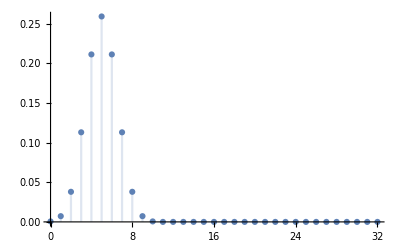

```mathematica
DiscretePlot[Table[PDF[HypergeometricDistribution[n,50,100],k],{n,{10}}]//Evaluate,{k,0,32},PlotRange->All]
```

```mathematica
PDF[HypergeometricDistribution[n,r,R],x]
```

Piecewise[{{(Binomial[r,x] Binomial[-r+R,n-x])/Binomial[R,n], 0≤x≤n&&n+r-R≤x≤n&&0≤x≤r&&n+r-R≤x≤r}, {0, True}}]

Let’s see the result when X and Y both follow Normal Distribution (just for fun)

```mathematica
(*Define the random variables*)
X=NormalDistribution[0,1];
Y=NormalDistribution[0,1];

Z=TransformedDistribution[x+y,{x\[Distributed]X,y\[Distributed]Y}];
(*Display the distribution of Z*)
Z
V=TransformedDistribution[x*y,{x\[Distributed]X,y\[Distributed]Y}];
V
W=TransformedDistribution[y/x,{x\[Distributed]X,y\[Distributed]Y}];
W
```

NormalDistribution[0,√2]

VarianceGammaDistribution[1/2,1,0,0]

CauchyDistribution[0,1]

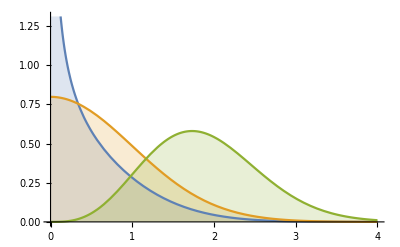

```mathematica
Plot[Table[PDF[ChiDistribution[ν],x],{ν,{.5,1,4}}]//Evaluate,{x,0,4},Filling->Axis]
```

```mathematica
PDF[ChiDistribution[ν],x]
```

Piecewise[{{(2^(1-ν/2) ⅇ^(-x^2/2) x^(-1+ν))/Gamma[ν/2], x>0}, {0, True}}]

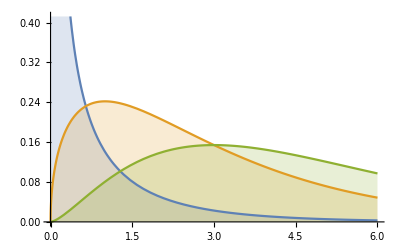

```mathematica
Plot[Table[PDF[ChiSquareDistribution[ν],x],{ν,{0.5,3,5}}]//Evaluate,{x,0,6},Filling->Axis]
```

```mathematica
PDF[ChiSquareDistribution[ν],x]
```

Piecewise[{{(2^(-ν/2) ⅇ^(-x/2) x^(-1+ν/2))/Gamma[ν/2], x>0}, {0, True}}]

```mathematica
X=ChiSquareDistribution[m];
Y=ChiSquareDistribution[n];
Z=TransformedDistribution[x+y,{x\[Distributed]X,y\[Distributed]Y}];
Z
```

ChiSquareDistribution[m+n]

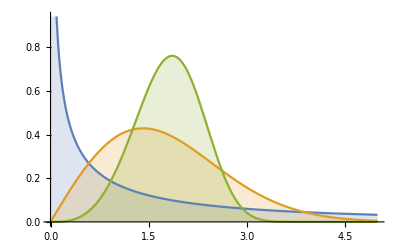

```mathematica
Plot[Table[PDF[WeibullDistribution[α,2],x],{α,{0.5,2,4}}]//Evaluate,{x,0,5},Filling->Axis]
```

```mathematica
PDF[WeibullDistribution[α,β,μ],x]
```

Piecewise[{{(ⅇ^(-((x-μ)/β)^α) α ((x-μ)/β)^(-1+α))/β, x>μ}, {0, True}}]

```mathematica
PDF[WeibullDistribution[α,β],x]
```

Piecewise[{{(ⅇ^(-(x/β)^α) α (x/β)^(-1+α))/β, x>0}, {0, True}}]

```mathematica
PDF[WeibullDistribution[β,1/α],x]
```

Piecewise[{{ⅇ^(-(x α)^β) α (x α)^(-1+β) β, x>0}, {0, True}}]